# MATRIX STRUCTURE

## For the coupling matrices to the LH fields of the S_1 leptoquark introducing a FN symmetry.

## Initialization and constants

```mathematica
hbar=6.582119*10^-25; (*GeV*s*)
secPerYear=3600*24*365.25;
hbary=hbar/secPerYear;

(* CKM and PMNS matrices *)
V= {{0.97435,0.22501,0.00373},{0.22487,0.97349,0.04183},{0.00858,0.04111,0.99912}};
U={{0.82296,0.54843,0.14815},{0.27528,0.61286,0.74069},{0.49695,0.56888,0.65531}};

(* 3rd generation charges *)
Qq3=0;
Ql3=0;

(* masses in GeV *)
mp=0.938272;
me=0.000511;
mmu=0.105658;
mpi0=0.134977;
mpiPlus=0.139570;
mK=0.493677;
meta = 0.54786;
mrho0=0.77503;
mrhoPlus=0.77511;
momega=0.78266;
mK0=0.49761;
mLQ=10000; (*10 TeV*)
Lambda= 10^16; (*GeV*) (* GUT scale *)

(* Renormalization group factor *)
AL = 1.4;
(* Lattice QCD form factor *)
W0benchmark=0.1;
W0EpiL= 0.134;
W0EpiR=-0.131;
W0MupiL=0.119;
W0MupiR=-0.118;
W0NupiL=0.189;
W0NupiR=-0.186;
W0NuKR=-0.134;
W0NuKL=0.139;
W0EetaR=0.006;
W0EetaL=0.113;
W0MuetaR=0.011;
W0MuetaL=0.108;


(* CM momentums: p=(1/(2mp))*Sqrt[(mp^2-mf1^2-mf2^2)^2-4*mf1^2*mf2^2] *)
pepi0=(1/(2*mp))*Sqrt[(mp^2-me^2-mpi0^2)^2-4*me^2*mpi0^2];
pmupi0=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mpi0^2)^2-4*mmu^2*mpi0^2];
pnupiPlus=(1/(2*mp))*(mp^2-mpiPlus^2);
pnuK=(1/(2*mp))*(mp^2-mK^2);
peeta=(1/(2*mp))*Sqrt[(mp^2-me^2-meta^2)^2-4*me^2*meta^2];
pmueta=(1/(2*mp))*Sqrt[(mp^2-mmu^2-meta^2)^2-4*mmu^2*meta^2];
perho=(1/(2*mp))*Sqrt[(mp^2-me^2-mrho0^2)^2-4*me^2*mrho0^2];
pmurho=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mrho0^2)^2-4*mmu^2*mrho0^2];
pnurho=(1/(2*mp))*(mp^2-mrhoPlus^2);
peomega=(1/(2*mp))*Sqrt[(mp^2-me^2-momega^2)^2-4*me^2*momega^2];
pmuomega=(1/(2*mp))*Sqrt[(mp^2-mmu^2-momega^2)^2-4*mmu^2*momega^2];
peK0=(1/(2*mp))*Sqrt[(mp^2-me^2-mK0^2)^2-4*me^2*mK0^2];
pmuK0=(1/(2*mp))*Sqrt[(mp^2-mmu^2-mK0^2)^2-4*mmu^2*mK0^2];

(* K prefactors assuming the leptoquark mass is inside this because we are taking it as a constant *)
KEpi0 = pepi0/(16*Pi*mp^2)*(AL^2 * W0EpiL^2)/mLQ^4*(mp^2+me^2-mpi0^2);
KMupi0= pmupi0/(16*Pi*mp^2)*(AL^2 * W0MupiL^2)/mLQ^4*(mp^2+mmu^2-mpi0^2);
KNupiPlus=pnupiPlus/(16*Pi*mp^2)*(AL^2 * W0NupiL^2)/mLQ^4*(mp^2-mpiPlus^2);
KNuK=pnuK/(16*Pi*mp^2)*(AL^2 * W0NuKL^2)/mLQ^4*(mp^2-mK^2);
KEeta=peeta/(16*Pi*mp^2)*(AL^2 * W0EetaL^2)/mLQ^4*(mp^2+me^2-meta^2);
KMueta=pmueta/(16*Pi*mp^2)*(AL^2 * W0MuetaL^2)/mLQ^4*(mp^2+mmu^2-meta^2);
KErho0= perho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+me^2-mrho0^2);
KMurho0=pmurho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+mmu^2-mrho0^2);
KNurhoPlus = pnurho/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2-mrhoPlus^2);
KEomega=peomega/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+me^2-momega^2);
KMuomega=pmuomega/(16*Pi*mp^2)*(AL^2 * W0benchmark^2)/mLQ^4*(mp^2+mmu^2-momega^2);
```

```mathematica
(* PDG experimental bounds (in years)*)
limEpi=2.4*10^34;
limMupi=1.6*10^34;
limNuPi=3.9*10^32;
limNuK=5.9*10^34;
limEeta=1.0*10^34;
limMueta=4.7*10^33;
limErho=7.2*10^32;
limMurho=5.7*10^32;
limNurho=1.62*10^32;
limEomega=1.6*10^33;
limMuomega=2.8*10^33;
```

## Monte Carlo scan

### Core

```mathematica
(*This function searches in the parameter space for variables that fit the PDG limits*)ScanProtonDecay[nLimits_,numSamples_,maxCharge_]:=Module[{results={},safetyFactors, minRobustness, bottleneckIdx, channelNames,bottleneck},
channelNames={"p->e^+π^0","p->μ^+π^0","p-> ν̄ π^+","p-> ν̄ K^+"};
Do[(*Assign random values to the exponents*)
{Qq1,Qq2,Ql1,Ql2}=RandomInteger[{-maxCharge,maxCharge},4];
eps=RandomReal[{10^-1,0.5}];

(*Reconstruct the coupling matrices*)y1LL={{eps^Abs[Qq1+Ql1],eps^Abs[Qq1+Ql2],eps^Abs[Qq1+Ql3]},{eps^Abs[Qq2+Ql1],eps^Abs[Qq2+Ql2],eps^Abs[Qq2+Ql3]},{eps^Abs[Qq3+Ql1],eps^Abs[Qq3+Ql2],1}};
z1LL={{eps^Abs[2*Qq1],eps^Abs[Qq1+Qq2],eps^Abs[Qq1+Qq3]},{eps^Abs[Qq1+Qq2],eps^Abs[2*Qq2],eps^Abs[Qq2+Qq3]},{eps^Abs[Qq1+Qq3],eps^Abs[Qq2+Qq3],1}};
(*Effective matrices*)
yEff=V.y1LL;
zEff=V.z1LL;
hEff=y1LL.U;

(*Recalculate lifetimes*)
tauEpi0=hbary/(KEpi0*Abs[zEff[[1,1]]*yEff[[1,1]]]^2);
tauMupi=hbary/(KMupi0*Abs[zEff[[1,1]]*yEff[[1,2]]]^2);
tauNuPi=hbary/(KNupiPlus*Abs[zEff[[1,1]]*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2);
tauNuK=hbary/(KNuK*Abs[zEff[[1,1]]*(hEff[[2,1]]+hEff[[2,2]]+hEff[[2,3]])]^2);
(*VEV calculation*)
Vev=eps*Lambda;(*GeV*)

(*Acumulative filter for each number of limits fulfilled*)isOk=Which[nLimits==1,tauEpi0>limEpi,nLimits==2,tauEpi0>limEpi&&tauMupi>limMupi,nLimits==3,tauEpi0>limEpi&&tauMupi>limMupi&&tauNuPi>limNuPi,nLimits==4,tauEpi0>limEpi&&tauMupi>limMupi&&tauNuPi>limNuPi&&tauNuK>limNuK];
If[isOk,
safetyFactors={tauEpi0/limEpi,tauMupi/limMupi,tauNuPi/limNuPi,tauNuK/limNuK};
minRobustness=Min[safetyFactors];
bottleneckIdx=Ordering[safetyFactors,1][[1]];
bottleneck=channelNames[[bottleneckIdx]];
AppendTo[results,{eps,Qq1,Qq2,Qq3,Ql1,Ql2,Ql3,Vev,minRobustness,bottleneck}]],{numSamples}];
Return[results]];
```

### Ejecution

```mathematica
(*Ejecution for x limits and y iterations*)
mysolutions=ScanProtonDecay[4,1000000,20];

Print["Number of solutions found: ",Length[mysolutions]];
sortedSolutions=SortBy[mysolutions,#[[9]] &];

If[Length[mysolutions]>0,TableForm[Take[sortedSolutions,Min[Length[sortedSolutions],10]],TableHeadings->{None,{"eps","Qq1","Qq2","Qq3","Ql1","Ql2","Ql3","vev","robustness factor","less robust channel"}}]]
```

Number of solutions found: 7025

eps | Qq1 | Qq2 | Qq3 | Ql1 | Ql2 | Ql3 | vev | robustness factor | less robust channel
0.10302 | -20 | -3 | 0 | 18 | 19 | 0 | 1.0302×10^15 | 1.00289 | p->μ^+π^0
0.175395 | -14 | -14 | 0 | -19 | -14 | 0 | 1.75395×10^15 | 1.00365 | p-> ν̄ K^+
0.132639 | 18 | 18 | 0 | -3 | 8 | 0 | 1.32639×10^15 | 1.00377 | p->e^+π^0
0.107229 | 18 | 18 | 0 | 1 | -7 | 0 | 1.07229×10^15 | 1.00478 | p->e^+π^0
0.132634 | 14 | 19 | 0 | 7 | 14 | 0 | 1.32634×10^15 | 1.00557 | p->e^+π^0
0.142325 | -14 | -11 | 0 | -15 | -17 | 0 | 1.42325×10^15 | 1.00568 | p-> ν̄ K^+
0.109056 | -17 | -12 | 0 | -20 | -2 | 0 | 1.09056×10^15 | 1.00633 | p->μ^+π^0
0.257131 | -19 | -17 | 0 | -18 | -12 | 0 | 2.57131×10^15 | 1.00887 | p->μ^+π^0
0.195569 | 20 | 14 | 0 | 6 | 16 | 0 | 1.95569×10^15 | 1.01465 | p->e^+π^0
0.101619 | 18 | 11 | 0 | -15 | 3 | 0 | 1.01619×10^15 | 1.01553 | p->e^+π^0

### Epsilon histogram

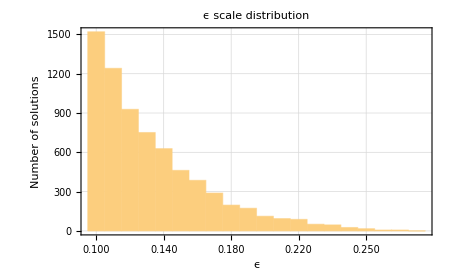

```mathematica
epsData=mysolutions[[All,1]];
minVal=Min[epsData];
maxVal=Max[epsData];
numBins=20;

(*Definimos los bordes y los centros de cada barra*)
binEdges=Subdivide[minVal,maxVal,numBins];
binCenters=Table[(binEdges[[i]]+binEdges[[i+1]])/2,{i,1,Length[binEdges]-1}];

(*Seleccionamos solo un tick de cada'step' (aquí de 4 en 4) para evitar que se amontonen*)
step=4;
customTicks=Table[{binCenters[[i]],NumberForm[binCenters[[i]],{2,3}]},{i,1,Length[binCenters],step}];

(*Generamos el histograma con los ticks limpios y espaciados*)
Histogram[epsData,{minVal,maxVal,(maxVal-minVal)/numBins},PlotLabel->"ϵ scale distribution",Frame->True,FrameLabel->{"ϵ","Number of solutions"},GridLines->Automatic,FrameTicks->{{Automatic,Automatic},{customTicks,Automatic}},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},LabelStyle->{FontSize->14,Bold},ImagePadding->{{45,15},{40,10}},ImageSize->450]
```

### Charge distribution

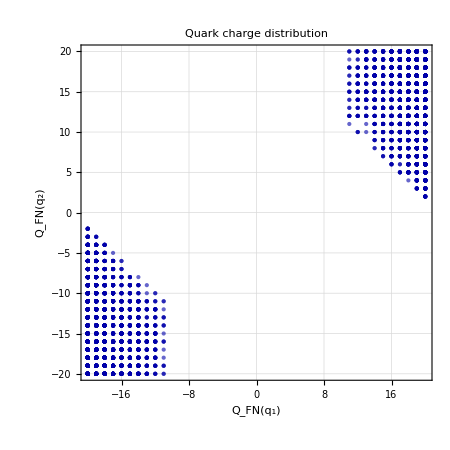

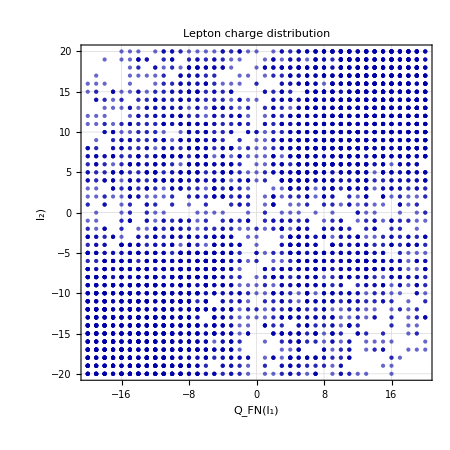

```mathematica
(*Charge extractions*)
qcharges=mysolutions[[All,{2,3}]];
lcharges=mysolutions[[All,{5,6}]];

(*Quark charge distribution plot*)
ListPlot[qcharges,PlotLabel->"Quark charge distribution",Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[\(q\), \(1\)]\))","\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[\(q\), \(2\)]\))"},GridLines->Automatic,PlotRange->{{-20,20},{-20,20}},AspectRatio->1,PlotStyle->Directive[PointSize[Medium],Darker[Blue],Opacity[0.6]],BaseStyle->{FontSize->14,FontFamily->"Helvetica"},LabelStyle->{FontSize->14,Bold},ImagePadding->{{45,15},{40,10}},ImageSize->450]


(*Lepton charge distribution plot*)
ListPlot[lcharges,PlotLabel->"Lepton charge distribution",Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(Q\), \(FN\)]\)(\!\(\*SubscriptBox[\(l\), \(1\)]\))","\!\(\*SubscriptBox[\(l\), \(2\)]\))"},GridLines->Automatic,PlotRange->{{-20,20},{-20,20}},AspectRatio->1,PlotStyle->Directive[PointSize[Medium],Darker[Blue],Opacity[0.6]],BaseStyle->{FontSize->14,FontFamily->"Helvetica"},LabelStyle->{FontSize->14,Bold},ImagePadding->{{45,15},{40,10}},ImageSize->450]
```

## Grid search

```mathematica
eps=0.1;
chargeLimit=20;
channelNames={"p->e^+π^0","p->μ^+π^0","p-> ν̄ π^+","p-> ν̄ K^+"};

totalIterations=0; 

(*Systematic grid search*)
gridResults=Reap[Do[totalIterations++;(*Reconstruct the coupling matrices*)y1LL={{eps^Abs[q1+l1],eps^Abs[q1+l2],eps^Abs[q1+Ql3]},{eps^Abs[q2+l1],eps^Abs[q2+l2],eps^Abs[q2+Ql3]},{eps^Abs[Qq3+l1],eps^Abs[Qq3+l2],1}};
z1LL={{eps^Abs[2*q1],eps^Abs[q1+q2],eps^Abs[q1+Qq3]},{eps^Abs[q1+q2],eps^Abs[2*q2],eps^Abs[q2+Qq3]},{eps^Abs[q1+Qq3],eps^Abs[q2+Qq3],1}};
(*Effective matrices and lifetime calculations*)
yEff=V.y1LL;
zEff=V.z1LL;
hEff=y1LL.U;

tauEpi0=hbary/(KEpi0*Abs[zEff[[1,1]]*yEff[[1,1]]]^2);
tauMupi=hbary/(KMupi0*Abs[zEff[[1,1]]*yEff[[1,2]]]^2);
tauNuPi=hbary/(KNupiPlus*Abs[zEff[[1,1]]*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2);
tauNuK=hbary/(KNuK*Abs[zEff[[1,1]]*(hEff[[2,1]]+hEff[[2,2]]+hEff[[2,3]])]^2);
(*Check PDG bounds*)
isOk=(tauEpi0>limEpi)&&(tauMupi>limMupi)&&(tauNuPi>limNuPi)&&(tauNuK>limNuK);
If[isOk,safetyFactors={tauEpi0/limEpi,tauMupi/limMupi,tauNuPi/limNuPi,tauNuK/limNuK};
minRobustness=Min[safetyFactors];
bottleneckIdx=Ordering[safetyFactors,1][[1]];
criticalChannel=channelNames[[bottleneckIdx]];
Sow[{q1,q2,l1,l2,minRobustness,criticalChannel}]],{q1,0,chargeLimit},{q2,0,chargeLimit},{l1,-chargeLimit,chargeLimit},{l2,-chargeLimit,chargeLimit}]];

(*Extract solutions and sort by robustness factor (tightest first)*)
allGridSolutions=If[Length[gridResults[[2]]]>0,gridResults[[2,1]],{}];
sortedGridSolutions=SortBy[allGridSolutions,#[[5]]&];

Print["Number of solutions found: ", Length[sortedGridSolutions], " → ", N[Length[sortedGridSolutions]/(totalIterations) *100], " % of the parameter space"]
(*Display the best solutions in an extended table format*)
If[Length[sortedGridSolutions]>0,TableForm[Take[sortedGridSolutions,Min[Length[sortedGridSolutions],5]],TableHeadings->{None,{"Q(q1)","Q(q2)","Q(l1)","Q(l2)","robustness factor","critical channel"}}],Print["No solutions found in this range."]]
```

Number of solutions found: 97729 → 13.1831 % of the parameter space

Q(q1) | Q(q2) | Q(l1) | Q(l2) | robustness factor | critical channel
20 | 2 | -18 | -19 | 1.54667 | p->μ^+π^0
20 | 2 | -17 | -19 | 1.54667 | p->μ^+π^0
20 | 2 | -16 | -19 | 1.54667 | p->μ^+π^0
20 | 2 | -15 | -19 | 1.54667 | p->μ^+π^0
20 | 2 | -14 | -19 | 1.54667 | p->μ^+π^0

### Robustness histogram

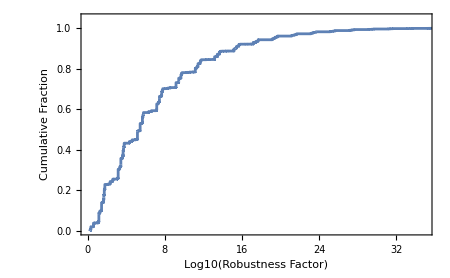

```mathematica
data=Log10[allGridSolutions[[All,5]]];
cdfData=Transpose[{Sort[data],Range[Length[data]]/Length[data]}];

ListLinePlot[cdfData,Frame->True,FrameLabel->{"Log10(Robustness Factor)","Cumulative Fraction"},PlotRange->{{0,35},{0,1.05}},
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},ImageSize->450]
```

## Visualization: interactive sliders

```mathematica
(*--- MANIPULATE ---*)
Manipulate[
(*Matrices Definition*)
y1LL={{eps^Abs[Qq1+Ql1],eps^Abs[Qq1+Ql2],eps^Abs[Qq1+Ql3]},{eps^Abs[Qq2+Ql1],eps^Abs[Qq2+Ql2],eps^Abs[Qq2+Ql3]},{eps^Abs[Qq3+Ql1],eps^Abs[Qq3+Ql2],1}};
z1LL={{eps^Abs[2*Qq1],eps^Abs[Qq1+Qq2],eps^Abs[Qq1+Qq3]},{eps^Abs[Qq1+Qq2],eps^Abs[2*Qq2],eps^Abs[Qq2+Qq3]},{eps^Abs[Qq1+Qq3],eps^Abs[Qq2+Qq3],1}};

(*Effective Matrices*)
yEff=V.y1LL;
zEff=V.z1LL;
hEff=y1LL.U;

(*Lifetime Calculations*)
tauEpi0=hbary/(KEpi0*Abs[zEff[[1,1]]*yEff[[1,1]]]^2);
tauMupi=hbary/(KMupi0*Abs[zEff[[1,1]]*yEff[[1,2]]]^2);
tauNuPi=hbary/(KNupiPlus*Abs[zEff[[1,1]]*(hEff[[1,1]]+hEff[[1,2]]+hEff[[1,3]])]^2);
tauNuK=hbary/(KNuK*Abs[zEff[[1,1]]*(hEff[[2,1]]+hEff[[2,2]]+hEff[[2,3]])]^2);
tauEeta=tauEpi0*KEpi0/KEeta;
tauMueta=tauMupi*KMupi0/KMueta;
tauErho=tauEpi0*KEpi0/KErho0;
tauMurho=tauMupi*KMupi0/KMurho0;
tauNurhoPlus=tauNuPi*KNupiPlus/KNurhoPlus;
tauEomega=tauEpi0*KEpi0/KEomega;
tauMuomega=tauMupi*KMupi0/KMuomega;

(*Visualization*)Column[{Style["Coupling Matrices (Flavor Basis)",Bold,16],Row[{Style["y1LL = ",14],MatrixForm[y1LL],Spacer[30],Style["z1LL = ",14],MatrixForm[z1LL]}],Spacer[20],Grid[{{Style["Results: Proton lifetime (years)",Bold,16]},{Grid[{{Style["Channel",Bold],Style["Theoretical Tau [years]",Bold],Style["PDG bound [years]",Bold],Style["Status",Bold]},{"p → e^+ π^0",ScientificForm[tauEpi0,3],ScientificForm[limEpi,3],If[tauEpi0>limEpi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → μ^+ π^0",ScientificForm[tauMupi,3],ScientificForm[limMupi,3],If[tauMupi>limMupi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → ν̄ π^+",ScientificForm[tauNuPi,3],ScientificForm[limNuPi,3],If[tauNuPi>limNuPi,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},{"p → ν̄ K^+",ScientificForm[tauNuK,3],ScientificForm[limNuK,3],If[tauNuK>limNuK,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → e^+ η",ScientificForm[tauEeta,3],ScientificForm[limEeta,3],If[tauEeta>limEeta,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → μ^+ η",ScientificForm[tauMueta,3],ScientificForm[limMueta,3],If[tauMueta>limMueta,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → e^+ ρ^0",ScientificForm[tauErho,3],ScientificForm[limErho,3],If[tauErho>limErho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → μ^+ ρ^0",ScientificForm[tauMurho,3],ScientificForm[limMurho,3],If[tauMurho>limMurho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → ν̄ ρ^+",ScientificForm[tauNurhoPlus,3],ScientificForm[limNurho,3],If[tauNurhoPlus>limNurho,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → e^+ ω",ScientificForm[tauEomega,3],ScientificForm[limEomega,3],If[tauEomega>limEomega,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]},
{"p → μ^+ ω",ScientificForm[tauMuomega,3],ScientificForm[limMuomega,3],If[tauMuomega>limMuomega,Style["OK",Green,Bold],Style["EXCLUDED",Red,Bold]]}},
Frame->All,Background->{None,{LightGray,White}},Alignment->Left]}}]}],

(*Explicit Controls*)
Delimiter,
Style["Global Parameters",Bold],{{eps,0.1,"ϵ"},0.01,1,Appearance->"Labeled"},
Style["Exponents y1LL",Bold],
{{Qq1,20,"Qq1"},-20,20,1,Appearance->"Labeled"},
{{Qq2,2,"Qq2"},-20,20,1,Appearance->"Labeled"},
{{Ql1,-18,"Ql1"},-20,20,1,Appearance->"Labeled"},
{{Ql2,-19,"Ql2"},-20,20,1,Appearance->"Labeled"},
ControlPlacement->Left,TrackedSymbols:>All]
```